Temperature dependance on the amount of CO_2

Pastolis Mantas

Grankovsky Vladimir

University College London

Most representative image

-Graphics-

Abstract

GOAL OF THE PROJECT: To find how do the amounts of CO_2 can influence the local temperature.
The local amounts CO_2 in some places (especially Urban ones) can be consistently higher than in others. Although the weather is very dynamic and inconsistent, it is interesting to see if there is any correlation between the temperature and amounts of CO_2 locally, so the heat might get trapped and increase the temperature.

SUMMARY OF WORK: The work could be divided in few steps:
1. Retrieving the data from OCO-2 NASA satellite, which measures amount of CO_2 globally.
2.Retrieving the weather data from Wolfram repository: the temperature data from weather stations, which date back to 1950s, were retrieved and plotted.
3. The measurements of CO_2 from OCO-2 satellite was retrieved: the measurements included points around all the globe.

RESULTS AND FUTURE  WORK: Only small amount (66) of reliable weather stations date back to 1950s. There was no increase in average temperature observed overall, however, this is obviously very small sample and it is very hard to predict any reliable results from such a small number of samples.

Everything above this bar is your poster. Make sure it fits on a single page. "Preview Poster"

Additional concise content for 2 minute presentation

-Graphics-

Everything above this bar is in your 2 minute presentation. "Preview Presentation"

Detailed Records of the Project

Main Results in Detail

Code

Provide one of:

https://github.com/laukinisgyvunelis/WSS17/blob/master/Final%20Project

## Initial data

```mathematica
rects={{{29.034,-105.307},{44.645,-88.845}},{{36.583,-80.117},{53.817,-53.5}},{{19.400000000000002,-89.424},{30.983,-74.633}},{{34.354,-117.286},{35.354,-116.286}},{{48.19,5.138},{59.377,13.902000000000001}},{{-5.174,55.022},{-4.174,56.022}},{{-4.533,31.944000000000003},{0.542,40.117}},{{57.25,-162.3},{70.634,-143.082}},{{38.262,-27.591},{39.262,-26.591}},{{25.765,49.652},{26.765,50.652}},{{51.383,-177.15},{51.383,-177.15}+1},{{53.214,174.617}-1,{53.214,174.617}},{{13.067,144.417},{14.067,145.417}},{{20.85,-158.433},{21.85,-157.433}},{{27.717000000000002,-177.867},{28.717000000000002,-176.867}},{{33.086,129.951},{36.248,140.28}},{{12.633000000000001,120.032},{26.856,128.268}},{{31.863999999999997,-65.179},{32.864,-64.179}},{{6.687,100.06700000000001},{18.45,107.167}},{{66.517,-51.189},{67.517,-50.189}},{{63.475,-23.088},{64.475,-22.088}},{{53.471000000000004,-101.59100000000001},{54.471000000000004,-100.59100000000001}}};
```

```mathematica
rectsPos={{{-105.307,29.034},{-88.845,44.645}},{{-80.117,36.583},{-53.5,53.817}},{{-89.424,19.400000000000002},{-74.633,30.983}},{{-117.286,34.354},{-116.286,35.354}},{{5.138,48.19},{13.902000000000001,59.377}},{{55.022,-5.174},{56.022,-4.174}},{{31.944000000000003,-4.533},{40.117,0.542}},{{-162.3,57.25},{-143.082,70.634}},{{-27.591,38.262},{-26.591,39.262}},{{49.652,25.765},{50.652,26.765}},{{-177.15,51.383},{-176.15,52.383}},{{173.617,52.214},{174.617,53.214}},{{144.417,13.067},{145.417,14.067}},{{-158.433,20.85},{-157.433,21.85}},{{-177.867,27.717000000000002},{-176.867,28.717000000000002}},{{129.951,33.086},{140.28,36.248}},{{120.032,12.633000000000001},{128.268,26.856}},{{-65.179,31.863999999999997},{-64.179,32.864}},{{100.06700000000001,6.687},{107.167,18.45}},{{-51.189,66.517},{-50.189,67.517}},{{-23.088,63.475},{-22.088,64.475}},{{-101.59100000000001,53.471000000000004},{-100.59100000000001,54.471000000000004}}};
rectsPos=Reverse[SortBy[rectsPos,Times@@(Total[#*{-1,1}]&/@Transpose[#])&]];
rectsPosT=Transpose/@rectsPos;
```

```mathematica
rectsNeg={{{15.283224654404961,28.3744709481079},{128.5445313050078,88.49463711538613}},{{-183.65274239538155,-89.63750248325994},{30.665325219403364,17.754315029273215}},{{-183.44671094485778,-89.59543313895746},{179.140662066306,-6.658525469482285}},{{-141.74045697825238,55.526976967033974},{-52.46650374534019,91.07837752562136}},{{141.20673430871886,14.879576501933977},{179.9918651326937,51.007327077465995}},{{8.39702251509732,54.9211784090776},{177.97814585207936,91.08819370595863}},{{-72.77057161721571,1.5870660138127695},{98.41519959566688,24.72380306872494}},{{-173.84217130403277,23.87820924824417},{-118.91783769413246,55.99815362322228}},{{108.18229903123657,-90.98310390241315},{179.13645513187575,11.487385039673754}},{{-52.563263237236,40.854591985789874},{3.320251422761863,62.1304617110537}},{{-63.5938453133582,1.5896615647999894},{48.60649825295362,37.02067240835309}}};
```

```mathematica
rectsNeg=Reverse[SortBy[rectsNeg,Times@@(Total[#*{-1,1}]&/@Transpose[#])&]];
```

```mathematica
rectsNegT=Transpose/@rectsNeg;
```

```mathematica
firstDay=Import[FileNameJoin[{baseDirectory,ToString[{2016,1}]<>".mx"}]];
```

```mathematica
vet4={Entity["WeatherStation","KSAT"],Entity["WeatherStation","KMSN"],Entity["WeatherStation","KCEF"],Entity["WeatherStation","KFSI"],Entity["WeatherStation","KLCH"],Entity["WeatherStation","KRCA"],Entity["WeatherStation","KVPS"],Entity["WeatherStation","KDAG"],Entity["WeatherStation","KCYS"],Entity["WeatherStation","KBTV"],Entity["WeatherStation","EDDF"],Entity["WeatherStation","EDDI"],Entity["WeatherStation","EDDS"],Entity["WeatherStation","ENZV"],Entity["WeatherStation","FSIA"],Entity["WeatherStation","HKJK"],Entity["WeatherStation","HKMO"],Entity["WeatherStation","HUEN"],Entity["WeatherStation","KADQ"],Entity["WeatherStation","KBET"],Entity["WeatherStation","KBIG"],Entity["WeatherStation","KBIX"],Entity["WeatherStation","KBOS"],Entity["WeatherStation","KFAI"],Entity["WeatherStation","KGKN"],Entity["WeatherStation","KLFI"],Entity["WeatherStation","KNAK"],Entity["WeatherStation","LPLA"],Entity["WeatherStation","MUGM"],Entity["WeatherStation","OEDR"],Entity["WeatherStation","PABA"],Entity["WeatherStation","PAED"],Entity["WeatherStation","PAEI"],Entity["WeatherStation","PAFB"],Entity["WeatherStation","PAKN"],Entity["WeatherStation","PASY"],Entity["WeatherStation","PGUA"],Entity["WeatherStation","PHIK"],Entity["WeatherStation","PMDY"],Entity["WeatherStation","RJFF"],Entity["WeatherStation","RJTC"],Entity["WeatherStation","RJTT"],Entity["WeatherStation","RJTY"],Entity["WeatherStation","ROAH"],Entity["WeatherStation","RODN"],Entity["WeatherStation","RPLC"],Entity["WeatherStation","RPLI"],Entity["WeatherStation","RPLL"],Entity["WeatherStation","RPLP"],Entity["WeatherStation","TXKF"],Entity["WeatherStation","VLVT"],Entity["WeatherStation","VTSH"],Entity["WeatherStation","VVTS"],Entity["WeatherStation","WMO48455"],Entity["WeatherStation","WMO48918"],Entity["WeatherStation","WMO70454"],Entity["WeatherStation","BGSF"],Entity["WeatherStation","BIKF"],Entity["WeatherStation","CWAR"],Entity["WeatherStation","CWYR"],Entity["WeatherStation","CYJT"],Entity["WeatherStation","CYOW"],Entity["WeatherStation","CYQD"],Entity["WeatherStation","CYQY"],Entity["WeatherStation","CYYB"],Entity["WeatherStation","CYYZ"]};
```

## Initial filtering functions

Valid points are defined as the ones, which start start at 684121000 sec after 1993 Jan 1 (agreed time) or 2014 September 6 and are measured in either Sample Glint or Sample Nadir mode:

```mathematica
pointValid=#⟦1⟧>684121000&&(#⟦2⟧=="Sample Glint"||#⟦2⟧=="Sample Nadir")&;
```

Coordinates of weather stations are then filtered: only the stations, which have at least few points every day since 1950 Jan 1 are included (66 of them overall):

```mathematica
vet4Coordinates=#["Coordinates"]&/@vet4;
```

The coordinates of these weather stations are clustered, so to make the filtering and data processing easier. The clustering was done in DBSCAN mode:

```mathematica
clustering2=FindClusters[GeoPosition/@vet4Coordinates,Method->"DBSCAN"];
```

```mathematica
GeoListPlot[clustering2]
```

-Graphics-

The rectangles around separate clusters were created, so to exclude all the rest of the points outside those rectangles:

```mathematica
MinMax/@Transpose[clustering2⟦1,All,1⟧];
rects=Transpose[MinMax/@Transpose[#]]+{-0.5,0.5}&/@clustering2⟦All,All,1⟧;
```

```mathematica
stationRects=Map[Reverse,Function[p,# 0.5{1,1}+p&/@{-1,1}]/@vet4Coordinates,{2}];
stationRectsT=Transpose/@stationRects;
```

The yellow rectangles then were made: in order to parse the data faster, any point, appearing on any of those rectangles would be immediately removed.

```mathematica
Show[GeoGraphics[Rectangle@@@Map[GeoPosition,rects,{2}]],GeoListPlot[clustering2]]
```

Measuring the distance from every point to the specific station and choosing the station station of minimum distance from each point:

```mathematica
stationDist[point_,station_]:=GeoDistance[{point⟦3⟧,point⟦4⟧},station]
```

```mathematica
allStationDist[point_]:=Min[stationDist[point,#]&/@vet4Coordinates]
```

## Rectangle functions

The rectangles were made in the following order:
1. Negative filtering: the points within the yellow rectangles are immediately removed:

```mathematica
totallyOutside[{lat_,lon_}]:=Or@@((#⟦1,1⟧≤lat≤#⟦1,2⟧&&#⟦2,1⟧≤lon≤#⟦2,2⟧)&/@rectsNegT)
```

2. Positive filtering: the points within the black rectangles are included:

```mathematica
kindaInside[{lat_,lon_}]:=Or@@((#⟦1,1⟧≤lat≤#⟦1,2⟧&&#⟦2,1⟧≤lon≤#⟦2,2⟧)&/@rectsPosT)
```

3. Positive filtering: the points within rectangles that vary 0.5° to all world directions are included in the final lists for data processing

```mathematica
veryInside[{lat_,lon_}]:=Or@@((#⟦1,1⟧≤lat≤#⟦1,2⟧&&#⟦2,1⟧≤lon≤#⟦2,2⟧)&/@stationRectsT)
```

## Filter data

Processing every point for each day: first the points passes the first filter, where the majority of the points are gathered, then the second filter, where only the points within black rectangles are gathered and eventually the final set of points is taken around the station.

```mathematica
processDay[yearday_]:=Block[{day,data},
If[MissingQ[allDaysUsefulData[yearday]],
day=Import[ToString[yearday]<>".mx"];data=Select[day,pointValid[#]&&(!totallyOutside[#⟦{4,3}⟧])&&kindaInside[#⟦{4,3}⟧]&&veryInside[#⟦{4,3}⟧]&];
allDaysUsefulData=Join[allDaysUsefulData,<|yearday->data|>];
Export["allDaysUsefulData.mx",allDaysUsefulData];
];
]
```

Then the function was run through every day. Finally, the map for all data was produced (for 124 750 data points):

```mathematica
Values[allDaysUsefulData]
```

```mathematica
allDaysJoined=Join@@Values[allDaysUsefulData];
allDaysJoined//Length
```

124750

```mathematica
GeoGraphics[Point[GeoPosition/@allDaysJoined⟦All,{3,4}⟧]]
```

-Graphics-

However, as this is not very representative, a separate station should be zoomed in to see the data points distribution:

```mathematica
GeoGraphics[{Opacity[0.6],Red,Point@*GeoPosition/@dataPerStation⟦#,All,{3,4}⟧,Blue,GeoDisk[vet4Coordinates⟦#⟧,Quantity[50,"Miles"]]},
GeoRange->Quantity[50,"Miles"],GeoCenter->vet4Coordinates⟦#⟧]&[38]
```

Data distribution around Berlin:

The amount of CO_2 averaged and ploted on the map around the weather stations:

```mathematica
GeoRegionValuePlot[Thread[(GeoDisk[GeoPosition[#],Quantity[150, "Miles"]]&/@vet4Coordinates)->1000000median],PlotLegends->Histogram,PlotRange->{395,407}]
```

After processing the CO_2 data, the weather data can be processed.

```mathematica
allWeatherStations=WeatherData[];
```

Retrieving only the weather stations that have a few data points every day since 1950 Jan 1st and plotting the average yearly temperature of every such weather station:

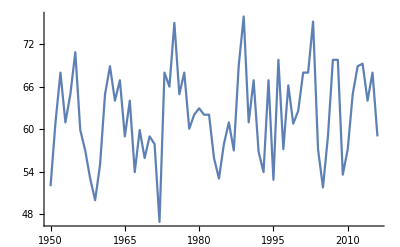

```mathematica
ListLinePlot[Transpose[{Range[1950,2016],yearlyT⟦6⟧}]]
```

Afterwards, the two data sets should be compared. The linear coefficient of yearly average temperature of every station was computed:

```mathematica
coef=(LinearModelFit[{#1,QuantityMagnitude[#2]}&@@@Select[Transpose[{Range[1950,2016],#}],!MissingQ[#⟦2⟧]&],x,x]&/@yearlyT)⟦All,1,2,2⟧
```

{0.00371378,0.0542189,0.0820265,0.0160782,0.00793586,0.0580557,0.0055168,0.0947859,0.0509784,0.0816632,0.103044,0.0820661,0.118003,0.0342412,0.0217804,0.105359,0.0403722,0.0276531,0.0477835,0.0347086,0.023233,0.00935989,0.0482361,0.0630625,0.040502,0.0282736,-0.0659128,0.00591188,0.040027,0.120001,0.106594,0.0421535,0.0864724,0.129447,0.0260252,0.052249,0.0353381,0.031032,0.027143,0.0352129,0.16812,0.0386357,0.0671354,0.0159072,0.0359843,-0.0118974,-0.0145698,0.0160264,0.0469458,0.0202098,0.0893197,0.032603,-0.0141009,0.0570599,0.00816991,0.0332818,0.0567717,0.0272904,0.0578431,0.0748964,0.102903,0.114452,0.0156321,0.0405842,0.0606741,0.0793137}

The value of coefficient (in y axis) was compared to the amount of CO2_2 around that station over 2014-2017 years. The following plot was obtained:

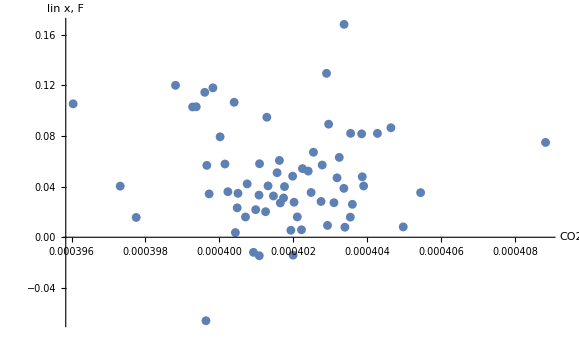

```mathematica
ListPlot[Transpose[{median,coef}],AxesLabel->{"CO2","lin x, F"}]
```

Hardly any correlation can be seen from the plot. Therefore, it is unlikely that there is any correlation between the local amount of CO_2 and the change in temperature, however, the model should be improved to include more data points, which would be accessible over the following years after 1950s.

Written Content / Lesson Plans

Conclusions in Detail

There was very little correlation found between the local amount of CO_2 and temperature change over the past 67 years. However, very few points were available and it is very hard to draw solid conclusions from that.
One thing to take into account is that the although very insignificant, there was seen some positive correlation of temperature increase over the last 67 years.
On the other hand, the amount of CO_2 in those places seemed not to correlate with the local temperature changes. While it is known that the weather is extremely dynamic, the hypothesis that the CO_2 locally would have some significance, especially in the areas with the high CO_2 emittance, where the carbon dioxide could potentially trap the heat and create micro climate for greenhouse effect.

All Visualizations

-Graphics-

-Graphics-

-Graphics-

-Graphics-

Data Sources Links/References

NASA database for OCO-2 satellite second level processed data:
https://oco2.gesdisc.eosdis.nasa.gov/data/s4pa/OCO2_DATA/OCO2_L2_Standard.7r/

Future Directions

Background Info Links/References

Keywords

Provide keywords as items

Climate science

Atmospheric chemistry

Climate Modelling

Statistics

Other

Date

Last Modified: Wednesday, July 05, 2017

```mathematica
"Add Timestamp"
```